# Scintillating Grid Illusion

### https : // mathworld . wolfram . com/ScintillatingGridIllusion . html

```mathematica
Manipulate[coor=Table[{i,j},{i,0,w},{j,0,h}];pts=Flatten[coor[[2;;-2,2;;-2]],1];line=coor[[2;;-2,{1,-1}]]~Join~Transpose@coor[[{1,-1},2;;-2]];
Graphics[{Black,Rectangle[{0,0},{w,h}],Gray,Thickness[lw],CapForm["Round"],Line[line],White,PointSize[ps],Point[pts]}],{{w,8,"Width"},3,10,1},{{h,5,"Height"},3,10,1},{{lw,0.02},0.001,0.1},{{ps,0.025},0.001,0.1}]
```

### 简化

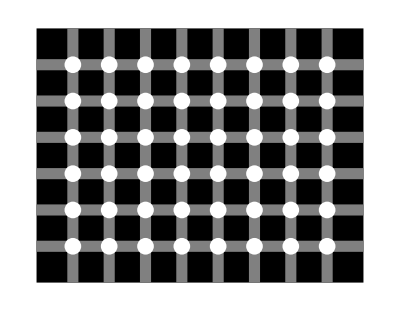

```mathematica
c=Table[{i,j},{i,0,9},{j,0,7}];p=Flatten[c[[2;;-2,2;;-2]],1];l=c[[2;;-2,{1,-1}]]~Join~Transpose@c[[{1,-1},2;;-2]];Graphics[{Black,Rectangle[{0,0},{9,7}],Gray,Thickness[.02],CapForm["Round"],Line[l],White,PointSize[.03],Point[p]}]
```